```mathematica
SetDirectory[NotebookDirectory[]];
<<P2Scattering`
<<CoulombHiggs`
(* <<MaTeX`*)
```

P2Scattering 1.5 - A package for evaluating DT invariants on K_(ℙ^2)

CoulombHiggs 6.3 - A package for evaluating quiver invariants

## The following routines are now part of P2Scattering 1.5:

```mathematica
ConstructMcKayDiagram::usage="ConstructMcKayDiagram[Nmax_,ListRays_] constructs the quiver scattering diagram with height up to Nmax; The output consists of a list of  {charge, {u,v}, parent1, parent2,n1,n2}  with parent1=parent2=0 for initial rays; If ListRays is not empty, then uses it as initial rays.";
McKayTreesFromListRays::usage="McKayTreesFromListRays[ListRays_,{n1_,n2_,n3_}] extracts the list of distinct trees with given dimension vector";
McKayScattIndexImproved::usage="McKayScattIndexImproved[TreeList_, opt_] computes the index for each tree in TreeList, taking care of non-primitive internal states";
McKayScattIndexImprovedInternal::usage="McKayScattIndexImprovedInternal[Tree_, opt_] computes the index for Tree, taking care of non-primitive internal states";
InitialRaysOrigin::usage ="InitialRaysOrigin is a List of initial points (u_i,v_i) for initial rays in McKay scattering diagram";
```

```mathematica
ConstructLVDiagram::usage="ConstructLVDiagram[smin_,smax_,phimax_,Nm_,ListRays_] constructs the LV scattering diagram with initial rays O(k),O(k)[1] in the interval smin<=k<=smax, cost function up to phimax, scattering products with n1+n2<=Nm at each intersection; the output consists of a list of {charge, {x,y}, parent1,parent2,n1,n2}, with parent1=parent2=0 for initial rays; If ListRays is not empty, then uses it as initial rays.";
```

```mathematica
LVTreesFromListRays::usage="lVTreesFromListRays[ListRays_,{r_,d_,chi_}] extract the trees with given charge in the List of rays,  by ConstructLVDiagram";
ScattIndexImproved::usage="ScattIndexImproved[TreeList_, opt_] computes the index for each tree in TreeList, taking care of non-primitive internal states";
ScattIndexImprovedInternal::usage="ScattIndexImprovedInternal[Tree_, opt_] computes the index for Tree, taking care of non-primitive internal states";
CostPhi::usage="CostPhi[{r_,d_,chi_},s_]:=d-r s";
```

```mathematica
KroneckerDims::usage="KroneckerDims[m_,Nn_] gives the list of populated dimension vectors {n1,n2} for Kronecker quiver with m arrows, with (n1,n2) coprime and 0<=n1+n2<=Nn"; 
FOmbToOm::usage="FOmbToOm[OmbList_] computes integer index from list of rational indices, used internally by FScattIndex";
```

```mathematica
ConstructLVDiagram[smin_,smax_,phimax_,Nm_,ListRays0_]:=Module[
{Inter,ListInter,ListRays,ListNewRays,kappa,KTab},
(* initial rays {charge, {x,y}, parent1, parent2,n1,n2 } *)
If[ListRays0=={},
         ListRays=Flatten[{
Table[{Ch[k],{k,-k^2/2},0,0,0,0},{k,Ceiling[smin],Floor[smax]}],
Table[{Ch[k][1],{k,-k^2/2},0,0,0,0},{k,Ceiling[smin],Floor[smax]}]},1]/.repCh;
   ListInter={};,
(* If list of rays is already provided *)
ListRays=ListRays0;
ListInter=Select[Table[{ListRays[[i,3]],ListRays[[i,4]]},{i,Length[ListRays]}],First[#]>0&]];
While[True,
ListNewRays={};
       Monitor[ Do[
If[  !MemberQ[ListInter,{i,j}],
AppendTo[ListInter,{i,j}];
 kappa=DSZ[ListRays[[i,1]],ListRays[[j,1]]];
If[kappa!=0,Inter=IntersectRaysNoTest[ListRays[[i,1]],ListRays[[j,1]],ListRays[[i,2]],ListRays[[j,2]]];
If[Inter!={},
KTab=KroneckerDims[Abs[kappa],Nm];
Do[If[CostPhi[KTab[[k,1]] ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter[[1]]]<=phimax,
AppendTo[ListNewRays,{KTab[[k,1]]ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter,i,j,KTab[[k,1]],KTab[[k,2]]}]],{k,Length[KTab]}]
]]]
,{i,Length[ListRays]},{j,i+1,Length[ListRays]}],{i,j}];
If[ListNewRays=={},Break[],
Print["Adding ",Length[ListNewRays], " rays, "];
ListRays=Flatten[{ListRays,ListNewRays},1];
]];
Print[Length[ListRays], " in total."];
ListRays];

(* Extract tree leading to k-th ray, internal *)
TreeFromListRays[ListRays_,k_]:=If[ListRays[[k,3]]==0,ListRays[[k,1]],{ListRays[[k,5]]TreeFromListRays[ListRays,ListRays[[k,3]]],ListRays[[k,6]]TreeFromListRays[ListRays,ListRays[[k,4]]]}];

(* Extract all trees leading to a ray with charge {r,d,chi} *)
LVTreesFromListRays[ListRays_,{r_,d_,chi_}]:=Module[{Lipos,Div,LiTrees},
Div=Divisors[GCD@@{r,d,chi}];
Lipos=Flatten[Join[Table[Position[ListRays,{r,d,chi}/k],{k,Div}]],1];
If[Lipos=={},
Print["No such dimension vector in the list"],
LiTrees=(GCD[r,d,chi]/GCD@@ListRays[[#,1]])TreeFromListRays[ListRays,#]&/@First[Transpose[Lipos]];
ScattSort[DeleteDuplicatesBy[SortBy[LiTrees,Length[TreeConstituents[#]]&],ScattGraph]
]]];

CostPhi[{r_,d_,chi_},s_]:=d-r s;

IntersectRaysNoTest[{r_,d_,chi_},{rr_,dd_,cchi_},z_,zz_]:=
(* returns (x,y) coordinate of intersection point of two rays, or {} if they don't intersect *)
(* here do not test if DSZ<>0, and require strictly in future of z and zz *)
Module[{zi},zi={(2 cchi r-3 dd r-2 chi rr+3 d rr)/(2 dd r-2 d rr),(cchi d-chi dd+dd r-d rr)/(-dd r+d rr)};
If[(zi-z) . {-r,d}>0&&(zi-zz) . {-rr,dd}>0,zi,{}]];

ClearAll[KroneckerDims];
KroneckerDims[m_,Nn_]:=KroneckerDims[m,Nn]=Module[{Ta={}},
Do[If[m n1 n2-n1^2-n2^2+1>=0&&GCD[n1,n2]==1,AppendTo[Ta,{n1,n2}]],{n1,0,Nn},{n2,0,Nn-n1}];Drop[Ta,2]];


(* construct scattering diagram up to height phimax
ConstructMcKayDiagram[phimax_,Nm_,ListRays0_]:=Module[{ListRays,ListInter,kappa,Inter,KTab,ListNewRays},
If[ListRays0=={},
(* initial rays {charge, {x,y}, parent1, parent2,n1,n2,level } *)
ListRays=Table[{IdentityMatrix[3][[k]],InitialRaysOrigin[[k]]-5 McKayVec[IdentityMatrix[3][[k]]],0,0,0,0,1},{k,3}];
ListInter={};,
(* If list of rays is already provided *)
ListRays=ListRays0;
ListInter=Select[Table[{ListRays[[i,3]],ListRays[[i,4]]},{i,Length[ListRays]}],First[#]>0&]];
While[True,
ListNewRays={};
       Monitor[ Do[
If[  !MemberQ[ListInter,{i,j}],
AppendTo[ListInter,{i,j}];
 kappa=McKayDSZ[ListRays[[i,1]],ListRays[[j,1]]];
If[kappa!=0,Inter=McKayIntersectRaysNoTest[ListRays[[i,1]],ListRays[[j,1]],ListRays[[i,2]],ListRays[[j,2]]];
If[Inter!={},
KTab=KroneckerDims[Abs[kappa],Nm];
Do[If[Plus@@(KTab[[k,1]] ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]])<=phimax,
AppendTo[ListNewRays,{KTab[[k,1]]ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter,i,j,KTab[[k,1]],KTab[[k,2]],ListRays[[i,7]]+ListRays[[j,7]]}]],{k,Length[KTab]}]
]]]
,{i,Length[ListRays]},{j,i+1,Length[ListRays]}],{i,j}];
If[ListNewRays=={},Break[],
Print["Adding ",Length[ListNewRays], " rays, "];
ListRays=Flatten[{ListRays,ListNewRays},1];
]];
Print[Length[ListRays], " in total."];
ListRays]; *)

InitialRaysOrigin={{1,0},{-1/2,-Sqrt[3]/2},{-1/2,Sqrt[3]/2}};

(* construct scattering diagram up to height phimax *)
ConstructMcKayDiagram[phimax_,ListRays0_]:=Module[{ListRays,ListInter,kappa,Inter,KTab,ListNewRays},
If[ListRays0=={},
(* initial rays {charge, {x,y}, parent1, parent2,n1,n2,level } *)
ListRays=Table[{IdentityMatrix[3][[k]],InitialRaysOrigin[[k]]-5 McKayVec[IdentityMatrix[3][[k]]],0,0,0,0,1},{k,3}];
ListInter={};,
(* If list of rays is already provided *)
ListRays=ListRays0;
ListInter=Select[Table[{ListRays[[i,3]],ListRays[[i,4]]},{i,Length[ListRays]}],First[#]>0&]];
While[True,
ListNewRays={};
       Monitor[ Do[
If[  !MemberQ[ListInter,{i,j}],
AppendTo[ListInter,{i,j}];
 kappa=McKayDSZ[ListRays[[i,1]],ListRays[[j,1]]];
If[kappa!=0,Inter=McKayIntersectRaysNoTest[ListRays[[i,1]],ListRays[[j,1]],ListRays[[i,2]],ListRays[[j,2]]];
If[Inter!={},
KTab=KroneckerDims[Abs[kappa],Floor[phimax/Min[Plus@@ListRays[[i,1]],Plus@@ListRays[[j,1]]]]];
Do[If[Plus@@(KTab[[k,1]] ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]])<=phimax,
AppendTo[ListNewRays,{KTab[[k,1]]ListRays[[i,1]]+KTab[[k,2]]ListRays[[j,1]],Inter,i,j,KTab[[k,1]],KTab[[k,2]],ListRays[[i,7]]+ListRays[[j,7]]}]],{k,Length[KTab]}]
]]]
,{i,Length[ListRays]},{j,i+1,Length[ListRays]}],{i,j}];
If[ListNewRays=={},Break[],
Print["Adding ",Length[ListNewRays], " rays, "];
ListRays=Flatten[{ListRays,ListNewRays},1];
]];
Print[Length[ListRays], " in total."];
ListRays];

McKayIntersectRaysNoTest[Nvec_,NNvec_,z_,zz_]:=
(* require strict inequality *)
Module[{zi},zi=McKayIntersectRays[Nvec,NNvec];If[(zi-z) . McKayVec[Nvec]>0&&(zi-zz) . McKayVec[NNvec]>0,zi,{}]];

(* Extract all trees leading up to a ray with dimension vector {n1,n2,n3} *)
McKayTreesFromListRays[ListRays_,{n1_,n2_,n3_}]:=Module[{Lipos,Div,LiTrees},
Div=Divisors[GCD@@{n1,n2,n3}];
Lipos=Flatten[Join[Table[Position[ListRays,{n1,n2,n3}/k],{k,Div}]],1];
If[Lipos=={},
Print["No such dimension vector in the list"],
LiTrees=((n1+n2+n3)/Plus@@ListRays[[#,1]])TreeFromListRays[ListRays,#]&/@First[Transpose[Lipos]];
ScattSort[DeleteDuplicatesBy[SortBy[LiTrees,Length[TreeConstituents[#]]&],McKayScattGraph]
]]];

(* more careful implementation taking care of internal non-primitive states *)
Options[McKayScattIndexImprovedInternal] = {"Debug"->False};

McKayScattIndexImproved[TreeList_, opt: OptionsPattern[]]:=Table[
	(* compute index for each tree in the list *)
	Simplify[FOmbToOm[Last@McKayScattIndexImprovedInternal[TreeList[[i]], opt][[2]]]],{i,Length[TreeList]}];

McKayScattIndexImprovedInternal[Tree_, opt: OptionsPattern[]]:=Module[{S1,S2,g1,g2,gFinal, kappa,Li, tem, repOmAttb, rrr},
(* compute {total charge, list of Kronecker indices associated to each vertex *)
	If[!ListQ[Tree]||Length[Tree]>2,{Tree,{Join[{1}, Table[(y-y^-1)/(j(y^j-y^-j)), {j, 2, GCD@@Tree}]]}},
	If[OptionValue["Debug"], Print["Calling with args: ", Tree[[1]], "  |  ", Tree[[2]]]];
S1=McKayScattIndexImprovedInternal[Tree[[1]], opt]/.repChn;
	S2=McKayScattIndexImprovedInternal[Tree[[2]], opt]/.repChn;
If[OptionValue["Debug"], Print["S1 is: ", S1, "   S2 is: ", S2]];
	g1=GCD@@S1[[1]];g2=GCD@@S2[[1]];
gFinal = GCD@@(S1[[1]]+S2[[1]]);
	kappa=Abs[McKayDSZ[S1[[1]],S2[[1]]]]/g1/g2;
	Li=Join[S1[[2]],S2[[2]]];
If[OptionValue["Debug"], Print["Li is: ", Li, "  g1 is: ", g1, "  g2 is: ", g2, "  gFinal is: ", gFinal]];
AppendTo[Li,
repOmAttb = Join[
Table[CoulombHiggs`OmAttb[{P, 0}, y_]->Last[S1[[2]]][[P]], {P, 1, g1}],
Table[CoulombHiggs`OmAttb[{0, Q}, y_]->Last[S2[[2]]][[Q]], {Q, 1, g2}]
];
If[OptionValue["Debug"], Print["repOmAttb is: ", repOmAttb]];
tem = Table[
rrr = If[And@@(IntegerQ/@{P g1/gFinal, P g2/gFinal}), CoulombHiggs`FlowTreeFormulaRat[{{0, kappa}, {-kappa, 0}}, {g2, -g1}, {P g1/gFinal, P g2/gFinal}, y], 0];
Simplify[
rrr
/.repOmAttb
/.{CoulombHiggs`OmAttb[{p_, q_}, y___]:>0/;p>1||q>1||p q !=0}
],
{P, 1, gFinal}
];
If[OptionValue["Debug"], Print["tem is: ", tem]];tem
];
	{S1[[1]]+S2[[1]],Li}]];

(* more careful implementation taking care of internal non-primitive states *)
Options[ScattIndexImprovedInternal] = {"Debug"->False};
ScattIndexImproved[TreeList_, opt: OptionsPattern[]]:=Table[
	(* compute index for each tree in the list *)
	Simplify[FOmbToOm[Last@ScattIndexImprovedInternal[TreeList[[i]], opt][[2]]]],{i,Length[TreeList]}];

ScattIndexImprovedInternal[Tree_, opt: OptionsPattern[]]:=Module[{S1,S2,g1,g2,gFinal, kappa,Li, tem, repOmAttb, rrr},
(* compute {total charge, list of Kronecker indices associated to each vertex *)
	If[!ListQ[Tree]||Length[Tree]>2,{Tree,{Join[{1}, Table[(y-y^-1)/(j(y^j-y^-j)), {j, 2, GCD@@(Tree/.repCh)}]]}},
	If[OptionValue["Debug"], Print["Calling with args: ", Tree[[1]], "  |  ", Tree[[2]]]];
    S1=ScattIndexImprovedInternal[Tree[[1]], opt]/.repCh;
	S2=ScattIndexImprovedInternal[Tree[[2]], opt]/.repCh;
If[OptionValue["Debug"], Print["S1 is: ", S1, "   S2 is: ", S2]];
	g1=GCD@@S1[[1]];g2=GCD@@S2[[1]];
    gFinal = GCD@@(S1[[1]]+S2[[1]]);
	kappa=3Abs[(S1[[1,1]]S2[[1,2]] -S1[[1,2]]S2[[1,1]])/g1/g2];
	Li=Join[S1[[2]],S2[[2]]];
If[OptionValue["Debug"], Print["Li is: ", Li, "  g1 is: ", g1, "  g2 is: ", g2, "  gFinal is: ", gFinal," kappa is",kappa]];
AppendTo[Li,
repOmAttb = Join[
Table[CoulombHiggs`OmAttb[{P, 0}, y_]->Last[S1[[2]]][[P]], {P, 1, g1}],
Table[CoulombHiggs`OmAttb[{0, Q}, y_]->Last[S2[[2]]][[Q]], {Q, 1, g2}]
];
If[OptionValue["Debug"], Print["repOmAttb is: ", repOmAttb]];
tem = Table[
rrr = If[And@@(IntegerQ/@{P g1/gFinal, P g2/gFinal}),CoulombHiggs`FlowTreeFormulaRat[{{0, kappa}, {-kappa, 0}}, {g2, -g1}, {P g1/gFinal, P g2/gFinal}, y], 0];
Simplify[
rrr
/.repOmAttb
/.{CoulombHiggs`OmAttb[{p_, q_}, y___]:>0/;p>1||q>1||p q !=0}
],
{P, 1, gFinal}
];
If[OptionValue["Debug"], Print["tem is: ", tem]];tem
];
	{S1[[1]]+S2[[1]],Li}]];

FOmbToOm[OmbList_] := Module[{n},
If[Length[OmbList]<2, First@OmbList, 
n = Length[OmbList];
DivisorSum[n, (MoebiusMu[#] (y-y^-1)/(#(y^#-y^-#)) (OmbList[[n/#]]/.{y->y^#}))&]
]];
```

## Large volume scattering diagram

```mathematica
ListRays=ConstructLVDiagram[-3,0,5,4,{}];
```

Adding 28 rays,

Adding 81 rays,

Adding 8 rays,

125 in total.

```mathematica
(* result for ConstructLVDiagram[-6,0,5,4,{}] in hidden cell below: *)
```

```mathematica
ListRays={{{1,-6,10},{-6,-18},0,0,0,0},{{1,-5,6},{-5,-25/2},0,0,0,0},{{1,-4,3},{-4,-8},0,0,0,0},{{1,-3,1},{-3,-9/2},0,0,0,0},{{1,-2,0},{-2,-2},0,0,0,0},{{1,-1,0},{-1,-1/2},0,0,0,0},{{1,0,1},{0,0},0,0,0,0},{{-1,6,-10},{-6,-18},0,0,0,0},{{-1,5,-6},{-5,-25/2},0,0,0,0},{{-1,4,-3},{-4,-8},0,0,0,0},{{-1,3,-1},{-3,-9/2},0,0,0,0},{{-1,2,0},{-2,-2},0,0,0,0},{{-1,1,0},{-1,-1/2},0,0,0,0},{{-1,0,-1},{0,0},0,0,0,0},{{0,1,-4},{-11/2,-15},2,8,1,1},{{-1,7,-14},{-11/2,-15},2,8,1,2},{{-2,13,-24},{-11/2,-15},2,8,1,3},{{1,-4,2},{-11/2,-15},2,8,2,1},{{2,-9,8},{-11/2,-15},2,8,3,1},{{0,2,-7},{-5,-12},3,8,1,1},{{-1,8,-17},{-5,-12},3,8,1,2},{{-2,14,-27},{-5,-12},3,8,1,3},{{1,-2,-4},{-5,-12},3,8,2,1},{{2,-6,-1},{-5,-12},3,8,3,1},{{0,1,-3},{-9/2,-10},3,9,1,1},{{-1,6,-9},{-9/2,-10},3,9,1,2},{{-2,11,-15},{-9/2,-10},3,9,1,3},{{1,-3,0},{-9/2,-10},3,9,2,1},{{2,-7,3},{-9/2,-10},3,9,3,1},{{0,3,-9},{-9/2,-9},4,8,1,1},{{-1,9,-19},{-9/2,-9},4,8,1,2},{{1,0,-8},{-9/2,-9},4,8,2,1},{{0,2,-5},{-4,-15/2},4,9,1,1},{{-1,7,-11},{-4,-15/2},4,9,1,2},{{-2,12,-17},{-4,-15/2},4,9,1,3},{{1,-1,-4},{-4,-15/2},4,9,2,1},{{2,-4,-3},{-4,-15/2},4,9,3,1},{{0,1,-2},{-7/2,-6},4,10,1,1},{{-1,5,-5},{-7/2,-6},4,10,1,2},{{-2,9,-8},{-7/2,-6},4,10,1,3},{{1,-2,-1},{-7/2,-6},4,10,2,1},{{2,-5,0},{-7/2,-6},4,10,3,1},{{0,4,-10},{-4,-6},5,8,1,1},{{0,3,-6},{-7/2,-5},5,9,1,1},{{-1,8,-12},{-7/2,-5},5,9,1,2},{{1,1,-6},{-7/2,-5},5,9,2,1},{{0,2,-3},{-3,-4},5,10,1,1},{{-1,6,-6},{-3,-4},5,10,1,2},{{-2,10,-9},{-3,-4},5,10,1,3},{{1,0,-3},{-3,-4},5,10,2,1},{{2,-2,-3},{-3,-4},5,10,3,1},{{0,1,-1},{-5/2,-3},5,11,1,1},{{-1,4,-2},{-5/2,-3},5,11,1,2},{{-2,7,-3},{-5/2,-3},5,11,1,3},{{1,-1,-1},{-5/2,-3},5,11,2,1},{{2,-3,-1},{-5/2,-3},5,11,3,1},{{0,5,-10},{-7/2,-3},6,8,1,1},{{0,4,-6},{-3,-5/2},6,9,1,1},{{0,3,-3},{-5/2,-2},6,10,1,1},{{-1,7,-6},{-5/2,-2},6,10,1,2},{{1,2,-3},{-5/2,-2},6,10,2,1},{{0,2,-1},{-2,-3/2},6,11,1,1},{{-1,5,-2},{-2,-3/2},6,11,1,2},{{-2,8,-3},{-2,-3/2},6,11,1,3},{{1,1,-1},{-2,-3/2},6,11,2,1},{{2,0,-1},{-2,-3/2},6,11,3,1},{{0,1,0},{-3/2,-1},6,12,1,1},{{-1,3,0},{-3/2,-1},6,12,1,2},{{-2,5,0},{-3/2,-1},6,12,1,3},{{1,0,0},{-3/2,-1},6,12,2,1},{{2,-1,0},{-3/2,-1},6,12,3,1},{{0,5,-5},{-5/2,0},7,9,1,1},{{0,4,-2},{-2,0},7,10,1,1},{{0,3,0},{-3/2,0},7,11,1,1},{{-1,6,-1},{-3/2,0},7,11,1,2},{{1,3,1},{-3/2,0},7,11,2,1},{{0,2,1},{-1,0},7,12,1,1},{{-1,4,1},{-1,0},7,12,1,2},{{-2,6,1},{-1,0},7,12,1,3},{{1,2,2},{-1,0},7,12,2,1},{{2,2,3},{-1,0},7,12,3,1},{{0,1,1},{-1/2,0},7,13,1,1},{{-1,2,1},{-1/2,0},7,13,1,2},{{-2,3,1},{-1/2,0},7,13,1,3},{{1,1,2},{-1/2,0},7,13,2,1},{{2,1,3},{-1/2,0},7,13,3,1},{{1,-3,-1},{-11/2,-14},3,15,1,1},{{1,-2,-5},{-11/2,-14},3,15,1,2},{{1,-1,-9},{-11/2,-14},3,15,1,3},{{2,-7,2},{-11/2,-14},3,15,2,1},{{0,3,-11},{-31/6,-38/3},3,16,1,1},{{-1,10,-25},{-31/6,-38/3},3,16,1,2},{{1,-1,-8},{-31/6,-38/3},3,16,2,1},{{-1,9,-21},{-51/10,-62/5},3,17,1,1},{{0,5,-18},{-51/10,-62/5},3,17,2,1},{{1,-2,-3},{-11/2,-12},4,15,1,1},{{1,-1,-7},{-11/2,-12},4,15,1,2},{{0,4,-13},{-19/4,-39/4},4,16,1,1},{{1,-1,-6},{-5,-21/2},4,20,1,1},{{0,5,-16},{-47/10,-48/5},4,21,1,1},{{1,-2,-2},{-9/2,-9},4,25,1,1},{{1,-1,-5},{-9/2,-9},4,25,1,2},{{1,0,-8},{-9/2,-9},4,25,1,3},{{2,-5,-1},{-9/2,-9},4,25,2,1},{{0,3,-8},{-25/6,-8},4,26,1,1},{{-1,9,-17},{-25/6,-8},4,26,1,2},{{1,0,-7},{-25/6,-8},4,26,2,1},{{-1,8,-14},{-41/10,-39/5},4,27,1,1},{{0,5,-13},{-41/10,-39/5},4,27,2,1},{{1,-1,-4},{-11/2,-9},5,15,1,1},{{0,5,-14},{-43/10,-33/5},5,16,1,1},{{1,0,-7},{-5,-8},5,20,1,1},{{1,-1,-3},{-9/2,-7},5,25,1,1},{{1,0,-6},{-9/2,-7},5,25,1,2},{{0,4,-9},{-15/4,-11/2},5,26,1,1},{{1,0,-5},{-4,-6},5,33,1,1},{{0,5,-11},{-37/10,-27/5},5,34,1,1},{{1,-1,-2},{-7/2,-5},5,38,1,1},{{1,0,-4},{-7/2,-5},5,38,1,2},{{1,1,-6},{-7/2,-5},5,38,1,3},{{2,-3,-2},{-7/2,-5},5,38,2,1},{{0,3,-5},{-19/6,-13/3},5,39,1,1},{{-1,8,-10},{-19/6,-13/3},5,39,1,2},{{1,1,-5},{-19/6,-13/3},5,39,2,1},{{-1,7,-8},{-31/10,-21/5},5,40,1,1},{{0,5,-8},{-31/10,-21/5},5,40,2,1},{{1,0,-3},{-9/2,-4},6,25,1,1},{{0,5,-9},{-33/10,-14/5},6,26,1,1},{{1,1,-5},{-4,-7/2},6,33,1,1},{{1,0,-2},{-7/2,-3},6,38,1,1},{{1,1,-4},{-7/2,-3},6,38,1,2},{{0,4,-5},{-11/4,-9/4},6,39,1,1},{{1,1,-3},{-3,-5/2},6,47,1,1},{{0,5,-6},{-27/10,-11/5},6,48,1,1},{{1,0,-1},{-5/2,-2},6,52,1,1},{{1,1,-2},{-5/2,-2},6,52,1,2},{{1,2,-3},{-5/2,-2},6,52,1,3},{{2,-1,-1},{-5/2,-2},6,52,2,1},{{0,3,-2},{-13/6,-5/3},6,53,1,1},{{-1,7,-4},{-13/6,-5/3},6,53,1,2},{{1,2,-2},{-13/6,-5/3},6,53,2,1},{{-1,6,-3},{-21/10,-8/5},6,54,1,1},{{0,5,-3},{-21/10,-8/5},6,54,2,1},{{1,1,-1},{-7/2,0},7,38,1,1},{{0,5,-4},{-23/10,0},7,39,1,1},{{1,2,-2},{-3,0},7,47,1,1},{{1,1,0},{-5/2,0},7,52,1,1},{{1,2,-1},{-5/2,0},7,52,1,2},{{0,4,-1},{-7/4,0},7,53,1,1},{{1,2,0},{-2,0},7,62,1,1},{{0,5,-1},{-17/10,0},7,63,1,1},{{1,1,1},{-3/2,0},7,67,1,1},{{1,2,1},{-3/2,0},7,67,1,2},{{1,3,1},{-3/2,0},7,67,1,3},{{2,1,2},{-3/2,0},7,67,2,1},{{0,3,1},{-7/6,0},7,68,1,1},{{-1,6,1},{-7/6,0},7,68,1,2},{{1,3,2},{-7/6,0},7,68,2,1},{{-1,5,1},{-11/10,0},7,69,1,1},{{0,5,2},{-11/10,0},7,69,2,1},{{-1,7,-13},{-9/2,-9},8,25,1,1},{{-1,8,-16},{-9/2,-9},8,25,1,2},{{-1,9,-19},{-9/2,-9},8,25,1,3},{{-2,13,-23},{-9/2,-9},8,25,2,1},{{0,3,-10},{-29/6,-11},8,28,1,1},{{1,0,-10},{-29/6,-11},8,28,1,2},{{-1,9,-20},{-29/6,-11},8,28,2,1},{{1,-1,-7},{-49/10,-57/5},8,29,1,1},{{0,5,-17},{-49/10,-57/5},8,29,2,1},{{-1,8,-15},{-4,-6},8,33,1,1},{{0,5,-14},{-43/10,-39/5},8,36,1,1},{{-1,7,-12},{-7/2,-3},8,38,1,1},{{-1,8,-14},{-7/2,-3},8,38,1,2},{{0,4,-11},{-17/4,-15/2},8,41,1,1},{{-1,8,-13},{-3,0},8,47,1,1},{{-1,7,-11},{-5/2,3},8,52,1,1},{{0,5,-11},{-37/10,-21/5},8,55,1,1},{{-1,6,-8},{-7/2,-5},9,38,1,1},{{-1,7,-10},{-7/2,-5},9,38,1,2},{{-1,8,-12},{-7/2,-5},9,38,1,3},{{-2,11,-14},{-7/2,-5},9,38,2,1},{{0,3,-7},{-23/6,-20/3},9,41,1,1},{{1,1,-8},{-23/6,-20/3},9,41,1,2},{{-1,8,-13},{-23/6,-20/3},9,41,2,1},{{1,0,-6},{-39/10,-7},9,42,1,1},{{0,5,-12},{-39/10,-7},9,42,2,1},{{-1,7,-9},{-3,-5/2},9,47,1,1},{{0,5,-9},{-33/10,-4},9,50,1,1},{{-1,6,-7},{-5/2,0},9,52,1,1},{{-1,7,-8},{-5/2,0},9,52,1,2},{{0,4,-7},{-13/4,-15/4},9,55,1,1},{{-1,7,-7},{-2,5/2},9,62,1,1},{{-1,6,-6},{-3/2,5},9,67,1,1},{{0,5,-6},{-27/10,-1},9,70,1,1},{{-1,5,-4},{-5/2,-2},10,52,1,1},{{-1,6,-5},{-5/2,-2},10,52,1,2},{{-1,7,-6},{-5/2,-2},10,52,1,3},{{-2,9,-7},{-5/2,-2},10,52,2,1},{{0,3,-4},{-17/6,-10/3},10,55,1,1},{{1,2,-5},{-17/6,-10/3},10,55,1,2},{{-1,7,-7},{-17/6,-10/3},10,55,2,1},{{1,1,-4},{-29/10,-18/5},10,56,1,1},{{0,5,-7},{-29/10,-18/5},10,56,2,1},{{-1,6,-4},{-2,0},10,62,1,1},{{0,5,-4},{-23/10,-6/5},10,65,1,1},{{-1,5,-3},{-3/2,2},10,67,1,1},{{-1,6,-3},{-3/2,2},10,67,1,2},{{0,4,-3},{-9/4,-1},10,70,1,1},{{-1,6,-2},{-1,4},10,77,1,1},{{-1,5,-2},{-1/2,6},10,82,1,1},{{0,5,-1},{-17/10,6/5},10,85,1,1},{{-1,4,-1},{-3/2,0},11,67,1,1},{{-1,5,-1},{-3/2,0},11,67,1,2},{{-1,6,-1},{-3/2,0},11,67,1,3},{{-2,7,-2},{-3/2,0},11,67,2,1},{{0,3,-1},{-11/6,-1},11,70,1,1},{{1,3,-1},{-11/6,-1},11,70,1,2},{{-1,6,-2},{-11/6,-1},11,70,2,1},{{1,2,-1},{-19/10,-6/5},11,71,1,1},{{0,5,-2},{-19/10,-6/5},11,71,2,1},{{-1,5,0},{-1,3/2},11,77,1,1},{{0,5,1},{-13/10,3/5},11,80,1,1},{{-1,4,0},{-1/2,3},11,82,1,1},{{-1,5,1},{-1/2,3},11,82,1,2},{{0,4,1},{-5/4,3/4},11,85,1,1},{{-1,3,1},{-1/2,1},12,82,1,1},{{-1,4,2},{-1/2,1},12,82,1,2},{{-1,5,3},{-1/2,1},12,82,1,3},{{-2,5,1},{-1/2,1},12,82,2,1},{{0,3,2},{-5/6,1/3},12,85,1,1},{{1,4,4},{-5/6,1/3},12,85,1,2},{{-1,5,2},{-5/6,1/3},12,85,2,1},{{1,3,3},{-9/10,1/5},12,86,1,1},{{0,5,3},{-9/10,1/5},12,86,2,1},{{1,-1,-8},{-11/2,-13},15,23,1,1},{{1,-2,-4},{-11/2,-13},15,28,1,1},{{1,-1,-8},{-11/2,-13},15,28,2,1},{{2,-6,-1},{-11/2,-27/2},15,29,1,1},{{1,-1,-5},{-11/2,-10},15,41,1,1},{{-1,9,-21},{-5,-23/2},16,20,1,1},{{0,5,-18},{-51/10,-61/5},16,23,1,1},{{-1,8,-17},{-9/2,-8},16,25,1,1},{{-1,9,-20},{-9/2,-8},16,25,1,2},{{0,4,-14},{-5,-23/2},16,28,1,1},{{-1,9,-19},{-4,-9/2},16,33,1,1},{{-1,8,-16},{-7/2,-1},16,38,1,1},{{0,5,-15},{-9/2,-8},16,41,1,1},{{-2,15,-31},{-5,-47/4},17,20,1,1},{{-2,14,-27},{-9/2,-17/2},17,25,1,1},{{1,-1,-7},{-5,-23/2},20,28,1,1},{{2,-5,-4},{-5,-47/4},20,29,1,1},{{1,0,-8},{-5,-9},20,41,1,1},{{-1,9,-20},{-9/2,-8},21,25,1,1},{{0,5,-17},{-49/10,-56/5},21,28,1,1},{{1,0,-7},{-9/2,-8},25,36,1,1},{{1,-1,-4},{-9/2,-8},25,41,1,1},{{1,0,-7},{-9/2,-8},25,41,2,1},{{2,-4,-3},{-9/2,-17/2},25,42,1,1},{{1,0,-4},{-9/2,-5},25,55,1,1},{{-1,8,-14},{-4,-7},26,33,1,1},{{0,5,-13},{-41/10,-38/5},26,36,1,1},{{-1,7,-11},{-7/2,-4},26,38,1,1},{{-1,8,-13},{-7/2,-4},26,38,1,2},{{0,4,-10},{-4,-7},26,41,1,1},{{-1,8,-12},{-3,-1},26,47,1,1},{{-1,7,-10},{-5/2,2},26,52,1,1},{{0,5,-10},{-7/2,-4},26,55,1,1},{{-2,13,-20},{-4,-29/4},27,33,1,1},{{-2,12,-17},{-7/2,-9/2},27,38,1,1},{{1,0,-6},{-4,-7},33,41,1,1},{{2,-3,-5},{-4,-29/4},33,42,1,1},{{1,1,-6},{-4,-9/2},33,55,1,1},{{-1,8,-13},{-7/2,-4},34,38,1,1},{{0,5,-12},{-39/10,-34/5},34,41,1,1},{{1,1,-5},{-7/2,-4},38,50,1,1},{{1,0,-3},{-7/2,-4},38,55,1,1},{{1,1,-5},{-7/2,-4},38,55,2,1},{{2,-2,-3},{-7/2,-9/2},38,56,1,1},{{1,1,-2},{-7/2,-1},38,70,1,1},{{-1,7,-8},{-3,-7/2},39,47,1,1},{{0,5,-8},{-31/10,-4},39,50,1,1},{{-1,6,-6},{-5/2,-1},39,52,1,1},{{-1,7,-7},{-5/2,-1},39,52,1,2},{{0,4,-6},{-3,-7/2},39,55,1,1},{{-1,7,-6},{-2,3/2},39,62,1,1},{{-1,6,-5},{-3/2,4},39,67,1,1},{{0,5,-5},{-5/2,-1},39,70,1,1},{{-2,11,-11},{-3,-15/4},40,47,1,1},{{-2,10,-9},{-5/2,-3/2},40,52,1,1},{{1,1,-4},{-3,-7/2},47,55,1,1},{{2,-1,-4},{-3,-15/4},47,56,1,1},{{1,2,-3},{-3,-1},47,70,1,1},{{-1,7,-7},{-5/2,-1},48,52,1,1},{{0,5,-7},{-29/10,-17/5},48,55,1,1},{{1,2,-2},{-5/2,-1},52,65,1,1},{{1,1,-1},{-5/2,-1},52,70,1,1},{{1,2,-2},{-5/2,-1},52,70,2,1},{{2,0,-1},{-5/2,-3/2},52,71,1,1},{{1,2,1},{-5/2,2},52,85,1,1},{{-1,6,-3},{-2,-1},53,62,1,1},{{0,5,-3},{-21/10,-7/5},53,65,1,1},{{-1,5,-2},{-3/2,1},53,67,1,1},{{-1,6,-2},{-3/2,1},53,67,1,2},{{0,4,-2},{-2,-1},53,70,1,1},{{-1,6,-1},{-1,3},53,77,1,1},{{-1,5,-1},{-1/2,5},53,82,1,1},{{0,5,0},{-3/2,1},53,85,1,1},{{-2,9,-4},{-2,-5/4},54,62,1,1},{{-2,8,-3},{-3/2,1/2},54,67,1,1},{{1,2,-1},{-2,-1},62,70,1,1},{{2,1,-1},{-2,-5/4},62,71,1,1},{{1,3,1},{-2,3/2},62,85,1,1},{{-1,6,-2},{-3/2,1},63,67,1,1},{{0,5,-2},{-19/10,-1},63,70,1,1},{{1,3,2},{-3/2,1},67,80,1,1},{{1,2,2},{-3/2,1},67,85,1,1},{{1,3,2},{-3/2,1},67,85,2,1},{{2,2,3},{-3/2,1/2},67,86,1,1},{{-1,5,1},{-1,1/2},68,77,1,1},{{0,5,2},{-11/10,1/5},68,80,1,1},{{-1,4,1},{-1/2,2},68,82,1,1},{{-1,5,2},{-1/2,2},68,82,1,2},{{0,4,2},{-1,1/2},68,85,1,1},{{-2,7,1},{-1,1/4},69,77,1,1},{{-2,6,1},{-1/2,3/2},69,82,1,1},{{1,3,3},{-1,1/2},77,85,1,1},{{2,3,4},{-1,1/4},77,86,1,1},{{-1,5,2},{-1/2,2},78,82,1,1},{{0,5,3},{-9/10,2/5},78,85,1,1},{{1,0,-9},{-29/6,-10},4,165,1,1},{{0,5,-13},{-41/10,-31/5},5,161,1,1},{{1,1,-7},{-23/6,-17/3},5,182,1,1},{{0,5,-8},{-31/10,-13/5},6,178,1,1},{{1,2,-4},{-17/6,-7/3},6,199,1,1},{{0,5,-3},{-21/10,0},7,195,1,1},{{1,3,0},{-11/6,0},7,216,1,1},{{-1,9,-18},{-25/6,-7},8,105,1,1},{{0,5,-12},{-39/10,-27/5},8,118,1,1},{{-1,8,-11},{-19/6,-10/3},9,122,1,1},{{0,5,-7},{-29/10,-2},9,135,1,1},{{-1,7,-5},{-13/6,-2/3},10,139,1,1},{{0,5,-2},{-19/10,2/5},10,152,1,1},{{-1,6,0},{-7/6,1},11,156,1,1},{{1,-1,-6},{-11/2,-11},15,101,1,1},{{0,5,-16},{-47/10,-47/5},16,101,1,1},{{1,0,-9},{-5,-10},20,101,1,1},{{1,0,-5},{-9/2,-6},25,118,1,1},{{0,5,-11},{-37/10,-26/5},26,118,1,1},{{1,1,-7},{-4,-11/2},33,118,1,1},{{-1,9,-18},{-4,-11/2},33,161,1,1},{{1,1,-3},{-7/2,-2},38,135,1,1},{{-1,8,-15},{-7/2,-2},38,161,1,1},{{0,5,-6},{-27/10,-2},39,135,1,1},{{0,5,-14},{-43/10,-38/5},41,161,1,1},{{1,2,-4},{-3,-2},47,135,1,1},{{-1,8,-11},{-3,-2},47,178,1,1},{{1,2,0},{-5/2,1},52,152,1,1},{{-1,7,-9},{-5/2,1},52,178,1,1},{{0,5,-1},{-17/10,1/5},53,152,1,1},{{0,5,-9},{-33/10,-19/5},55,178,1,1},{{1,3,0},{-2,1/2},62,152,1,1},{{-1,7,-5},{-2,1/2},62,195,1,1},{{-1,6,-4},{-3/2,3},67,195,1,1},{{0,5,-4},{-23/10,-1},70,195,1,1},{{-1,6,0},{-1,2},77,212,1,1},{{-1,5,0},{-1/2,4},82,212,1,1},{{0,5,1},{-13/10,4/5},85,212,1,1}};
```

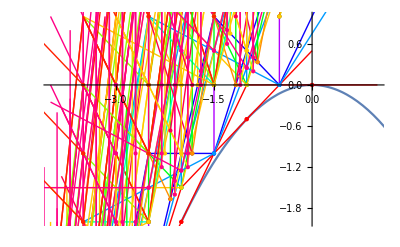

```mathematica
ClearAll[Rayxy];
(* redefine Rayxy such that second argument is z={x,y} *)
Rayxy[{r_,d_,chi_},{x0_,y0_},L_]:=
{Hue[1-(CostPhi[{r,d,chi},x0])/4.6],Point[{x0,y0}],Line[{{x0,y0},{x0-r L,y0+L d}}]};Show[Plot[-1/2s^2,{s,-2,2},PlotRange->{{-4,1},{-2,1}}],Graphics[Table[Rayxy[ListRays[[i,1]],ListRays[[i,2]],1],{i,Length[ListRays]}]]]
```

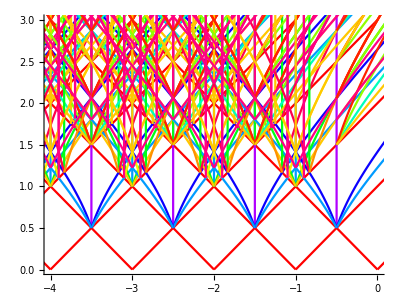

```mathematica
(* same in s,t coordinates *)
RayLV[{r_,d_,chi_},{x0_,y0_},L_,psi_]:=Module[{s0,t0},{s0,t0}=xytost[{x0,y0}];
If[Im[t0]!=0,t0=0];
ParametricPlot[Tooltip[{Rays[{r,d,chi},t,psi],t},"["<>ToString[r]<>","<>ToString[d]<>","<>ToString[chi]<>"]"],{t,t0,t0+3},PlotStyle->Hue[1-(CostPhi[{r,d,chi},x0])/4.6]]];
Show[Table[RayLV[ListRays[[i,1]],ListRays[[i,2]],1,0],{i,Length[ListRays]}],PlotRange->{{-4,-0},{0,3}}]
```

```mathematica
With[{gam={1,0,-4}},
LiTrees=LVTreesFromListRays[ListRays,gam];
Index=ScattIndexImproved[LiTrees];
{Series[EvaluateKronecker[Plus@@Index],{y,Infinity,0}],Series[Index,{y,1,0}]}
]
```

{y^10+2 y^8+6 y^6+11 y^4+19 y^2+21+O[1/y]^1,{27+O[y-1]^1,72+O[y-1]^1}}

```mathematica
LiTrees/.{{r_Integer,d_Integer,chi_Integer}:>If[r==0,GV[d,chi],If[Disc[{r,d,chi}]==0,If[r>0,r Ch[d/r],-r Ch[d/r][1]],{r,d,chi}]]}
```

{{{Ch[-4],Ch[-5][1]},{2 Ch[-2],Ch[-3][1]}},{Ch[-2],{2 Ch[-3],2 Ch[-4][1]}}}

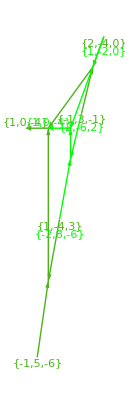

```mathematica
Show[ScattDiag[LiTrees]]
```

```mathematica
(* naive index *)
Index=ScattIndex[LiTrees];
{Series[EvaluateKronecker[Plus@@Index],{y,Infinity,0}],
Series[EvaluateKronecker[Index],{y,1,0}]}
```

Beware, non-primitive state

{-y^7+y^6-2 y^5+3 y^4-3 y^3+6 y^2-3 y+7+O[1/y]^1,{27+O[y-1]^1,-18+O[y-1]^1}}

## McKay scattering diagram

```mathematica
ListRays=ConstructMcKayDiagram[5,{}];
```

Adding 21 rays,

Adding 9 rays,

33 in total.

```mathematica
(* result for ConstructMcKayDiagram[10,{}] in hidden cell below *)
```

```mathematica
ListRays={{{1,0,0},{1+5 √3,5},0,0,0,0,1},{{0,1,0},{-1/2,-10-(√3)/2},0,0,0,0,1},{{0,0,1},{-1/2-5 √3,5+(√3)/2},0,0,0,0,1},{{1,1,0},{-1/2,-(√3)/2},1,2,1,1,2},{{1,2,0},{-1/2,-(√3)/2},1,2,1,2,2},{{1,3,0},{-1/2,-(√3)/2},1,2,1,3,2},{{2,1,0},{-1/2,-(√3)/2},1,2,2,1,2},{{2,3,0},{-1/2,-(√3)/2},1,2,2,3,2},{{2,5,0},{-1/2,-(√3)/2},1,2,2,5,2},{{3,1,0},{-1/2,-(√3)/2},1,2,3,1,2},{{3,2,0},{-1/2,-(√3)/2},1,2,3,2,2},{{3,4,0},{-1/2,-(√3)/2},1,2,3,4,2},{{3,5,0},{-1/2,-(√3)/2},1,2,3,5,2},{{3,7,0},{-1/2,-(√3)/2},1,2,3,7,2},{{4,3,0},{-1/2,-(√3)/2},1,2,4,3,2},{{4,5,0},{-1/2,-(√3)/2},1,2,4,5,2},{{5,2,0},{-1/2,-(√3)/2},1,2,5,2,2},{{5,3,0},{-1/2,-(√3)/2},1,2,5,3,2},{{5,4,0},{-1/2,-(√3)/2},1,2,5,4,2},{{7,3,0},{-1/2,-(√3)/2},1,2,7,3,2},{{1,0,1},{1,0},1,3,1,1,2},{{1,0,2},{1,0},1,3,1,2,2},{{1,0,3},{1,0},1,3,1,3,2},{{2,0,1},{1,0},1,3,2,1,2},{{2,0,3},{1,0},1,3,2,3,2},{{2,0,5},{1,0},1,3,2,5,2},{{3,0,1},{1,0},1,3,3,1,2},{{3,0,2},{1,0},1,3,3,2,2},{{3,0,4},{1,0},1,3,3,4,2},{{3,0,5},{1,0},1,3,3,5,2},{{3,0,7},{1,0},1,3,3,7,2},{{4,0,3},{1,0},1,3,4,3,2},{{4,0,5},{1,0},1,3,4,5,2},{{5,0,2},{1,0},1,3,5,2,2},{{5,0,3},{1,0},1,3,5,3,2},{{5,0,4},{1,0},1,3,5,4,2},{{7,0,3},{1,0},1,3,7,3,2},{{0,1,1},{-1/2,(√3)/2},2,3,1,1,2},{{0,1,2},{-1/2,(√3)/2},2,3,1,2,2},{{0,1,3},{-1/2,(√3)/2},2,3,1,3,2},{{0,2,1},{-1/2,(√3)/2},2,3,2,1,2},{{0,2,3},{-1/2,(√3)/2},2,3,2,3,2},{{0,2,5},{-1/2,(√3)/2},2,3,2,5,2},{{0,3,1},{-1/2,(√3)/2},2,3,3,1,2},{{0,3,2},{-1/2,(√3)/2},2,3,3,2,2},{{0,3,4},{-1/2,(√3)/2},2,3,3,4,2},{{0,3,5},{-1/2,(√3)/2},2,3,3,5,2},{{0,3,7},{-1/2,(√3)/2},2,3,3,7,2},{{0,4,3},{-1/2,(√3)/2},2,3,4,3,2},{{0,4,5},{-1/2,(√3)/2},2,3,4,5,2},{{0,5,2},{-1/2,(√3)/2},2,3,5,2,2},{{0,5,3},{-1/2,(√3)/2},2,3,5,3,2},{{0,5,4},{-1/2,(√3)/2},2,3,5,4,2},{{0,7,3},{-1/2,(√3)/2},2,3,7,3,2},{{1,1,2},{5/2,(√3)/2},1,39,1,1,3},{{1,2,4},{5/2,(√3)/2},1,39,1,2,3},{{1,3,6},{5/2,(√3)/2},1,39,1,3,3},{{2,1,2},{5/2,(√3)/2},1,39,2,1,3},{{3,1,2},{5/2,(√3)/2},1,39,3,1,3},{{3,2,4},{5/2,(√3)/2},1,39,3,2,3},{{1,1,3},{7/4,(√3)/4},1,40,1,1,3},{{1,2,6},{7/4,(√3)/4},1,40,1,2,3},{{2,1,3},{7/4,(√3)/4},1,40,2,1,3},{{3,1,3},{7/4,(√3)/4},1,40,3,1,3},{{4,1,3},{7/4,(√3)/4},1,40,4,1,3},{{5,1,3},{7/4,(√3)/4},1,40,5,1,3},{{6,1,3},{7/4,(√3)/4},1,40,6,1,3},{{1,2,3},{4,√3},1,42,1,1,3},{{2,2,3},{4,√3},1,42,2,1,3},{{3,2,3},{4,√3},1,42,3,1,3},{{1,2,5},{2,1/(√3)},1,43,1,1,3},{{2,2,5},{2,1/(√3)},1,43,2,1,3},{{3,2,5},{2,1/(√3)},1,43,3,1,3},{{1,3,4},{11/2,(3 √3)/2},1,46,1,1,3},{{2,3,4},{11/2,(3 √3)/2},1,46,2,1,3},{{3,3,4},{11/2,(3 √3)/2},1,46,3,1,3},{{1,3,5},{13/4,(3 √3)/4},1,47,1,1,3},{{2,3,5},{13/4,(3 √3)/4},1,47,2,1,3},{{1,4,5},{7,2 √3},1,50,1,1,3},{{2,1,1},{-1/2,-(3 √3)/2},2,24,1,1,3},{{4,1,2},{-1/2,-(3 √3)/2},2,24,1,2,3},{{6,1,3},{-1/2,-(3 √3)/2},2,24,1,3,3},{{2,2,1},{-1/2,-(3 √3)/2},2,24,2,1,3},{{2,3,1},{-1/2,-(3 √3)/2},2,24,3,1,3},{{4,3,2},{-1/2,-(3 √3)/2},2,24,3,2,3},{{3,1,1},{-1/2,-√3},2,27,1,1,3},{{6,1,2},{-1/2,-√3},2,27,1,2,3},{{3,2,1},{-1/2,-√3},2,27,2,1,3},{{3,3,1},{-1/2,-√3},2,27,3,1,3},{{3,4,1},{-1/2,-√3},2,27,4,1,3},{{3,5,1},{-1/2,-√3},2,27,5,1,3},{{3,6,1},{-1/2,-√3},2,27,6,1,3},{{3,1,2},{-1/2,-(5 √3)/2},2,28,1,1,3},{{3,2,2},{-1/2,-(5 √3)/2},2,28,2,1,3},{{3,3,2},{-1/2,-(5 √3)/2},2,28,3,1,3},{{4,1,3},{-1/2,-(7 √3)/2},2,32,1,1,3},{{4,2,3},{-1/2,-(7 √3)/2},2,32,2,1,3},{{4,3,3},{-1/2,-(7 √3)/2},2,32,3,1,3},{{5,1,2},{-1/2,-7/(2 √3)},2,34,1,1,3},{{5,2,2},{-1/2,-7/(2 √3)},2,34,2,1,3},{{5,3,2},{-1/2,-7/(2 √3)},2,34,3,1,3},{{5,1,3},{-1/2,-2 √3},2,35,1,1,3},{{5,2,3},{-1/2,-2 √3},2,35,2,1,3},{{5,1,4},{-1/2,-(9 √3)/2},2,36,1,1,3},{{1,2,1},{-2,√3},3,5,1,1,3},{{2,4,1},{-2,√3},3,5,1,2,3},{{3,6,1},{-2,√3},3,5,1,3,3},{{1,2,2},{-2,√3},3,5,2,1,3},{{1,2,3},{-2,√3},3,5,3,1,3},{{2,4,3},{-2,√3},3,5,3,2,3},{{1,3,1},{-5/4,(3 √3)/4},3,6,1,1,3},{{2,6,1},{-5/4,(3 √3)/4},3,6,1,2,3},{{1,3,2},{-5/4,(3 √3)/4},3,6,2,1,3},{{1,3,3},{-5/4,(3 √3)/4},3,6,3,1,3},{{1,3,4},{-5/4,(3 √3)/4},3,6,4,1,3},{{1,3,5},{-5/4,(3 √3)/4},3,6,5,1,3},{{1,3,6},{-5/4,(3 √3)/4},3,6,6,1,3},{{2,3,1},{-7/2,(3 √3)/2},3,8,1,1,3},{{2,3,2},{-7/2,(3 √3)/2},3,8,2,1,3},{{2,3,3},{-7/2,(3 √3)/2},3,8,3,1,3},{{2,5,1},{-3/2,5/(2 √3)},3,9,1,1,3},{{2,5,2},{-3/2,5/(2 √3)},3,9,2,1,3},{{2,5,3},{-3/2,5/(2 √3)},3,9,3,1,3},{{3,4,1},{-5,2 √3},3,12,1,1,3},{{3,4,2},{-5,2 √3},3,12,2,1,3},{{3,4,3},{-5,2 √3},3,12,3,1,3},{{3,5,1},{-11/4,(5 √3)/4},3,13,1,1,3},{{3,5,2},{-11/4,(5 √3)/4},3,13,2,1,3},{{4,5,1},{-13/2,(5 √3)/2},3,16,1,1,3},{{3,2,1},{-2,-√3},1,83,1,1,4},{{4,2,1},{-2,-√3},1,83,2,1,4},{{5,2,1},{-2,-√3},1,83,3,1,4},{{3,3,1},{-5/4,-(3 √3)/4},1,84,1,1,4},{{4,3,1},{-5/4,-(3 √3)/4},1,84,2,1,4},{{5,3,1},{-5/4,-(3 √3)/4},1,84,3,1,4},{{6,3,1},{-5/4,-(3 √3)/4},1,84,4,1,4},{{5,3,2},{-7/2,-(3 √3)/2},1,85,1,1,4},{{4,2,1},{-2,-√3},1,88,1,1,4},{{5,2,1},{-2,-√3},1,88,2,1,4},{{6,2,1},{-2,-√3},1,88,3,1,4},{{4,3,1},{-5/4,-(3 √3)/4},1,89,1,1,4},{{5,3,1},{-5/4,-(3 √3)/4},1,89,2,1,4},{{6,3,1},{-5/4,-(3 √3)/4},1,89,3,1,4},{{4,4,1},{-1,-2/(√3)},1,90,1,1,4},{{5,4,1},{-1,-2/(√3)},1,90,2,1,4},{{4,5,1},{-7/8,-(5 √3)/8},1,91,1,1,4},{{4,3,2},{-7/2,-(3 √3)/2},1,95,1,1,4},{{5,3,2},{-7/2,-(3 √3)/2},1,95,2,1,4},{{2,2,3},{4,√3},1,109,1,1,4},{{3,2,3},{4,√3},1,109,2,1,4},{{4,2,3},{4,√3},1,109,3,1,4},{{2,3,4},{11/2,(3 √3)/2},1,115,1,1,4},{{3,3,4},{11/2,(3 √3)/2},1,115,2,1,4},{{2,3,5},{13/4,(3 √3)/4},1,116,1,1,4},{{3,2,2},{-1/2,-(5 √3)/2},2,59,1,1,4},{{3,3,2},{-1/2,-(5 √3)/2},2,59,2,1,4},{{3,4,2},{-1/2,-(5 √3)/2},2,59,3,1,4},{{4,2,3},{-1/2,-(7 √3)/2},2,65,1,1,4},{{4,3,3},{-1/2,-(7 √3)/2},2,65,2,1,4},{{5,2,3},{-1/2,-2 √3},2,66,1,1,4},{{1,3,2},{-1/2,(3 √3)/2},2,108,1,1,4},{{1,4,2},{-1/2,(3 √3)/2},2,108,2,1,4},{{1,5,2},{-1/2,(3 √3)/2},2,108,3,1,4},{{1,3,3},{-1/2,√3},2,109,1,1,4},{{1,4,3},{-1/2,√3},2,109,2,1,4},{{1,5,3},{-1/2,√3},2,109,3,1,4},{{1,6,3},{-1/2,√3},2,109,4,1,4},{{2,5,3},{-1/2,(5 √3)/2},2,110,1,1,4},{{1,4,2},{-1/2,(3 √3)/2},2,113,1,1,4},{{1,5,2},{-1/2,(3 √3)/2},2,113,2,1,4},{{1,6,2},{-1/2,(3 √3)/2},2,113,3,1,4},{{1,4,3},{-1/2,√3},2,114,1,1,4},{{1,5,3},{-1/2,√3},2,114,2,1,4},{{1,6,3},{-1/2,√3},2,114,3,1,4},{{1,4,4},{-1/2,5/(2 √3)},2,115,1,1,4},{{1,5,4},{-1/2,5/(2 √3)},2,115,2,1,4},{{1,4,5},{-1/2,(3 √3)/4},2,116,1,1,4},{{2,4,3},{-1/2,(5 √3)/2},2,120,1,1,4},{{2,5,3},{-1/2,(5 √3)/2},2,120,2,1,4},{{2,1,3},{5/2,-(√3)/2},3,58,1,1,4},{{2,1,4},{5/2,-(√3)/2},3,58,2,1,4},{{2,1,5},{5/2,-(√3)/2},3,58,3,1,4},{{3,1,3},{7/4,-(√3)/4},3,59,1,1,4},{{3,1,4},{7/4,-(√3)/4},3,59,2,1,4},{{3,1,5},{7/4,-(√3)/4},3,59,3,1,4},{{3,1,6},{7/4,-(√3)/4},3,59,4,1,4},{{3,2,5},{4,-√3},3,60,1,1,4},{{2,1,4},{5/2,-(√3)/2},3,63,1,1,4},{{2,1,5},{5/2,-(√3)/2},3,63,2,1,4},{{2,1,6},{5/2,-(√3)/2},3,63,3,1,4},{{3,1,4},{7/4,-(√3)/4},3,64,1,1,4},{{3,1,5},{7/4,-(√3)/4},3,64,2,1,4},{{3,1,6},{7/4,-(√3)/4},3,64,3,1,4},{{4,1,4},{3/2,-1/(2 √3)},3,65,1,1,4},{{4,1,5},{3/2,-1/(2 √3)},3,65,2,1,4},{{5,1,4},{11/8,-(√3)/8},3,66,1,1,4},{{3,2,4},{4,-√3},3,70,1,1,4},{{3,2,5},{4,-√3},3,70,2,1,4},{{2,3,2},{-7/2,(3 √3)/2},3,84,1,1,4},{{2,3,3},{-7/2,(3 √3)/2},3,84,2,1,4},{{2,3,4},{-7/2,(3 √3)/2},3,84,3,1,4},{{3,4,2},{-5,2 √3},3,90,1,1,4},{{3,4,3},{-5,2 √3},3,90,2,1,4},{{3,5,2},{-11/4,(5 √3)/4},3,91,1,1,4},{{3,4,1},{-2,0},4,84,1,1,5},{{4,5,1},{-2,0},4,84,2,1,5},{{4,5,1},{-2,0},4,90,1,1,5},{{3,5,2},{-7/2,(5 √3)/2},5,119,1,1,5},{{2,5,1},{-2,2 √3},6,105,1,1,5},{{2,5,2},{-3/2,7/(2 √3)},6,108,1,1,5},{{2,5,3},{-7/5,√3},6,109,1,1,5},{{4,3,1},{-7/2,-(√3)/2},7,83,1,1,5},{{4,4,1},{-3/2,-(√3)/2},7,84,1,1,5},{{5,4,1},{-2,-(√3)/2},7,89,1,1,5},{{5,3,1},{-11/4,-(3 √3)/4},10,83,1,1,5},{{5,4,1},{-7/5,-(3 √3)/5},10,84,1,1,5},{{6,3,1},{-5,-√3},10,88,1,1,5},{{5,4,1},{-5,0},11,83,1,1,5},{{4,1,3},{1,-√3},21,59,1,1,5},{{5,1,4},{1,-√3},21,59,2,1,5},{{5,1,4},{1,-√3},21,65,1,1,5},{{3,1,4},{5/2,-(3 √3)/2},22,58,1,1,5},{{4,1,4},{3/2,-(√3)/2},22,59,1,1,5},{{4,1,5},{7/4,-(3 √3)/4},22,64,1,1,5},{{3,1,5},{5/2,-√3},23,58,1,1,5},{{4,1,5},{8/5,-(2 √3)/5},23,59,1,1,5},{{3,1,6},{4,-2 √3},23,63,1,1,5},{{5,2,3},{-2,-3 √3},24,94,1,1,5},{{4,1,5},{5/2,-(5 √3)/2},25,58,1,1,5},{{5,1,2},{-2,-2 √3},27,80,1,1,5},{{5,2,2},{-1,-4/(√3)},27,83,1,1,5},{{5,3,2},{-4/5,-(6 √3)/5},27,84,1,1,5},{{1,3,4},{1,√3},38,109,1,1,5},{{1,4,5},{1,√3},38,109,2,1,5},{{1,4,5},{1,√3},38,115,1,1,5},{{2,3,5},{11/2,(√3)/2},39,69,1,1,5},{{1,2,5},{4,0},40,55,1,1,5},{{2,2,5},{5/2,1/(2 √3)},40,58,1,1,5},{{3,2,5},{11/5,(√3)/5},40,59,1,1,5},{{1,4,3},{1,2 √3},41,108,1,1,5},{{1,4,4},{0,√3},41,109,1,1,5},{{1,5,4},{1/4,(5 √3)/4},41,114,1,1,5},{{1,5,3},{1/4,(7 √3)/4},44,108,1,1,5},{{1,5,4},{-1/5,√3},44,109,1,1,5},{{1,6,3},{1,3 √3},44,113,1,1,5},{{1,5,4},{5/2,(5 √3)/2},45,108,1,1,5},{{3,2,5},{5/2,0},58,61,1,1,6},{{5,3,2},{-5/4,-(5 √3)/4},83,86,1,1,6},{{2,5,3},{-5/4,(5 √3)/4},108,111,1,1,6},{{4,3,2},{-7/2,-(3 √3)/2},1,156,1,1,5},{{5,3,2},{-7/2,-(3 √3)/2},1,156,2,1,5},{{4,4,2},{-2,-√3},1,157,1,1,5},{{3,3,4},{11/2,(3 √3)/2},1,201,1,1,5},{{2,3,4},{11/2,(3 √3)/2},1,233,1,1,6},{{3,3,4},{11/2,(3 √3)/2},1,233,2,1,6},{{4,3,3},{-1/2,-(7 √3)/2},2,151,1,1,5},{{2,4,3},{-1/2,(5 √3)/2},2,200,1,1,5},{{2,5,3},{-1/2,(5 √3)/2},2,200,2,1,5},{{2,4,4},{-1/2,(3 √3)/2},2,201,1,1,5},{{4,2,3},{-1/2,-(7 √3)/2},2,219,1,1,6},{{4,3,3},{-1/2,-(7 √3)/2},2,219,2,1,6},{{3,2,4},{4,-√3},3,150,1,1,5},{{3,2,5},{4,-√3},3,150,2,1,5},{{4,2,4},{5/2,-(√3)/2},3,151,1,1,5},{{3,4,3},{-5,2 √3},3,157,1,1,5},{{3,4,2},{-5,2 √3},3,205,1,1,6},{{3,4,3},{-5,2 √3},3,205,2,1,6},{{3,5,2},{-7/2,(5 √3)/2},5,199,1,1,6},{{5,4,1},{-2,-(√3)/2},7,133,1,1,6},{{6,3,1},{-5,-√3},10,130,1,1,6},{{4,1,5},{7/4,-(3 √3)/4},22,183,1,1,6},{{3,1,6},{4,-2 √3},23,180,1,1,6},{{5,2,3},{-2,-3 √3},24,155,1,1,6},{{2,3,5},{11/2,(√3)/2},39,149,1,1,6},{{1,5,4},{1/4,(5 √3)/4},41,164,1,1,6},{{1,6,3},{1,3 √3},44,161,1,1,6}};
```

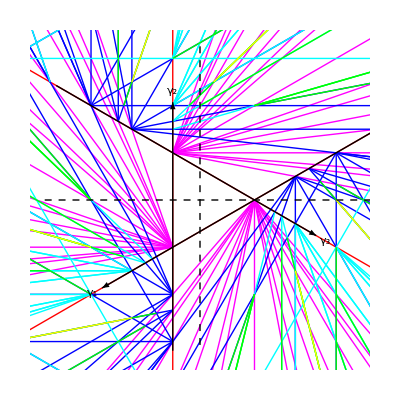

```mathematica
With[{L=3},Show[Graphics[Table[{Hue[1-(ListRays[[k,7]]-1)/6],McKayRay[ListRays[[k,1]],ListRays[[k,2]],{0,25},""]},{k,Length[ListRays]}]],McKayInitialRays[.95],PlotRange->{{-L,L},{-L,L}}]]
```

```mathematica
With[{gam={2,3,3}},
LiTrees=McKayTreesFromListRays[ListRays,gam];
Index=McKayScattIndexImproved[LiTrees];
Series[EvaluateKronecker[Plus@@Index],{y,Infinity,0}]
]
```

y^6+2 y^4+5 y^2+6+O[1/y]^1

```mathematica
LiTrees/.McKayrep
```

{{2 γ_3,{3 γ_2,{2 γ_1,γ_3}}},{3 γ_3,{2 γ_1,3 γ_2}}}

```mathematica
Index
```

{((1+y^2+y^4)^2)/y^4,3+1/y^6+1/y^4+3/y^2+3 y^2+y^4+y^6}

```mathematica
With[{gam={0,2,2}},
LiTrees=McKayTreesFromListRays[ListRays,gam];
Index=McKayScattIndexImproved[LiTrees];
Series[EvaluateKronecker[Plus@@Index],{y,Infinity,0}]
]
```

-y^5-y^3-y+O[1/y]^1

```mathematica
(* naive index *)
Series[EvaluateKronecker[Plus@@McKayScattIndex[LiTrees]],{y,Infinity,0}]
```

y^6+2 y^4+5 y^2+6+O[1/y]^1